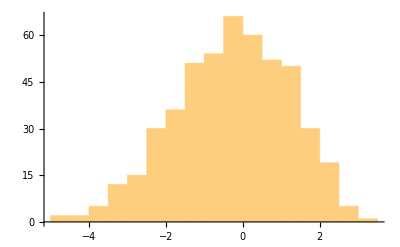

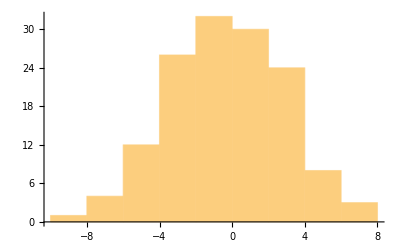

```mathematica
(* Histogram of eigenvalues *)
Es=Transpose[Import["G:\\LAT\\ExDiag\\data\\E_L8_h1.0000.dat"]][[1]];
Histogram[Es]
Es=Transpose[Import["G:\\LAT\\ExDiag\\data\\E_L8_h4.0000.dat"]][[1]];
Histogram[Es]
```

```mathematica
L=8; NN=2^L;
σs={({{0, 1}, {1, 0}}),({{0, -ⅈ}, {ⅈ, 0}}),({{1, 0}, {0, -1}})}; Id=({{1, 0}, {0, 1}});
(* Matrix implementation *)
ssm[a_,i_]:=Module[{σa,iψ},
σa={{1}};
For[iψ=L,iψ>i,iψ--,
σa=KroneckerProduct[σa,Id];
];
σa=KroneckerProduct[σa,σs[[a]]];
For[iψ=i-1,iψ≥1,iψ--,
σa=KroneckerProduct[σa,Id];
];
σa
];
h=Flatten[Import["G:\\LAT\\ExDiag\\hi.dat"]];
Print[h];
sssm=Sum[
in=If[i<L,i+1,1];
1/4(ssm[1,i].ssm[1,in] + ssm[2,i].ssm[2,in] + ssm[3,i].ssm[3,in])+h[[i]] ssm[3,i]
,{i,1,L}];
sssc=Import["G:\\LAT\\ExDiag\\H.dat"];
Print["|M1 - M2| = ",Norm[sssm-sssc,"Frobenius"]];
{evm,evs}=Eigensystem[sssm];
evc=Flatten[Import["G:\\LAT\\ExDiag\\E.dat"]];
Print[evc];
(* Checking the spin-0 sector *)
evs0={};
For[ie=1,ie≤NN,ie++,
R=sssm.evs[[ie]]-evm[[ie]] evs[[ie]];
SZ=Sum[evs[[ie]].ssm[3,i].evs[[ie]],{i,1,L}];
If[Abs[SZ]<10^-10,AppendTo[evs0,evm[[ie]] ];];
];
Print[Sort[evs0]," ",Sort[evc]];
Print["Eigenvalue error: ",Norm[Sort[evs0]-Sort[evc]]];
```

```mathematica
(* Algorithmic implementations to test *)
ss[ψ_,a_,i_]:=Module[{bmi,iψ1,iψ2,f1,f2},
(* Bit mask with 1 at position i *)
bmi=2^(i-1);
f1=1; f2=1;
If[a==2,f1=ⅈ; f2=-ⅈ];
If[a==3,f1=-1];
Table[
iψ2=If[a==3,iψ1,BitXor[bmi,iψ1]];
If[BitAnd[iψ1,bmi]≠0,f1,f2] ψ[[iψ2+1]]
,{iψ1,0,NN-1}]
];
ss1ss2[ψ_,a_,i_]:=Module[{in,bmi1,bmi2,iψ1,iψ2,f1,f2},
in=If[i<L,i+1,1];
bmi1=2^(i-1);
bmi2=2^(in-1);
f1=1;f2=1;
If[a==3,f1=-1];
If[a==2,f2=-1];
Table[
iψ2=If[a==3,iψ1,BitXor[bmi2,BitXor[bmi1,iψ1]]];
If[Xor[(BitAnd[iψ1,bmi1]≠0),(BitAnd[iψ1,bmi2]≠0)],f1,f2] ψ[[iψ2+1]],
{iψ1,0,NN-1}]
];
sss[ψ_]:=Module[{i,in,bmi1,bmi2,iψ1,iψ2,f1,f2,f3,C1},
Sum[
in=If[i<L,i+1,1];
bmi1=2^(i-1);
bmi2=2^(in-1);
Table[
C1=Xor[(BitAnd[iψ1,bmi1]≠0),(BitAnd[iψ1,bmi2]≠0)];
iψ2=BitXor[bmi2,BitXor[bmi1,iψ1]];
If[C1,2ψ[[iψ2+1]],0]+If[C1,-1,1] ψ[[iψ1+1]]
,{iψ1,0,NN-1}],
{i,1,L}]
];
(* Matrix implementations *)
ψ=Table[
SS=IntegerString[iψ,2,L];
Symbol["ψ"<>SS]
,{iψ,0,NN-1}];
(*MaxErr=0.0;
For[itrial=1,itrial≤100,itrial++,*)
R1=sssm.ψ;
Print[MatrixForm[sssm]];
R2=sss[ψ];
Print["Err = ",Norm[R1-R2]];
(*MaxErr=Max[MaxErr,Norm[R1-R2]];
];
Print[MaxErr];*)
```

```mathematica
MatrixForm[Table[{2n,((2n)!)/(n! n!),2^(2n)},{n,1,16}]]
```

```mathematica
L=24;
NN=2^L;
cnt=0;
For[ips=0, ips<NN, ips++,
bts=IntegerDigits[ips,2,L];
n0=Count[bts,0];
n1=Count[bts,1];
If[n0==n1,cnt++];
];
Print[cnt];
```